```mathematica
S1 =Sum[x^(m-n),{m,1,M},{n,0,m-1}]/.{x ->Cos[ω-β/2]/Cos[ω]}//FullSimplify
```

(-1-M+M Cos[ω] Sec[1/2 (β-2 ω)]+(Cos[1/2 (β-2 ω)] Sec[ω])^M)/(-1+Cos[ω] Sec[1/2 (β-2 ω)])^2

```mathematica
S2 =Sum[1,{m,1,M},{n,0,m-1}]
```

1/2 M (1+M)

```mathematica
JJ =FullSimplify[Tan[ω]^2 S2 - Tan[ω-β/2]^2 S1]/.M->N
```

-((-1-N+N Cos[ω] Sec[1/2 (β-2 ω)]+(Cos[1/2 (β-2 ω)] Sec[ω])^N) Tan[1/2 (β-2 ω)]^2)/(-1+Cos[ω] Sec[1/2 (β-2 ω)])^2+1/2 N (1+N) Tan[ω]^2

```mathematica
Numerator[JJ[[1]]]//FullSimplify
```

-((-1-N+N Cos[ω] Sec[1/2 (β-2 ω)]+(Cos[1/2 (β-2 ω)] Sec[ω])^N) Tan[1/2 (β-2 ω)]^2)

```mathematica
JJ[[2]]
```

1/2 N (1+N) Tan[ω]^2

```mathematica
Denominator[JJ[[1]]]
```

(-1+Cos[ω] Sec[1/2 (β-2 ω)])^2

```mathematica
Integrate[ Exp[-  M ω^2/2] /(ω +x),{ω, -Infinity,Infinity}]
```

ConditionalExpression[ⅇ^(-(M x^2)/2) (π Erfi[(√M x)/(√2)]-Log[-1/x]-Log[x]), Re[M]>0&&Im[x]≠0]

```mathematica
ClearAll[M,ϵ,Q];
```

```mathematica
PP =FullSimplify[ϵ^2/(32 Pi M)Exp[-Q^2/(2 M)](Integrate[ Exp[- M ω^2/2] /(ω +y),{ω, -Infinity,Infinity}]/.y -> ϵ + I Q/M),{ϵ >0, Q > 0, M >0}]
```

(ⅇ^(-1/2 ϵ (2 ⅈ Q+M ϵ)) ϵ^2 (π Erfi[(ⅈ Q+M ϵ)/(√2 √M)]-Log[-1/(ⅈ Q+M ϵ)]-Log[ⅈ Q+M ϵ]))/(32 M π)

```mathematica
pq =BinaryReadList["/Users/am10485/PycharmProjects/LoopEquations/plots/RandomFractions/Pairs.10000000000.np","Integer64"];
```

```mathematica
Dimensions[pq]
```

{20000000}

```mathematica
pq =ArrayReshape[pq,{10000000,2}];
```

```mathematica
Dimensions[pq]
```

{10000000,2}

```mathematica
pq[[1]]
```

{4427079041,8855258144}

```mathematica
pq[[-1]]
```

{1726099327,3451700328}

```mathematica
{p, q }= N[Transpose[pq],16];
```

```mathematica
{Dimensions[p], Dimensions[q]}
```

{{10000000},{10000000}}

```mathematica
Q = Downsample[q,10]/10000000000;
```

```mathematica
Qsmall = Sort[Q];
```

```mathematica
Dimensions[Qsmall]
```

{1000000}

```mathematica
Qsmall[[1]]
```

2.×10^-10

```mathematica
Qsmall[[-1]]
```

0.999999688

```mathematica
fitdata=ParallelTable[{Qsmall[[i]], Log[1 - (i - 0.5)/Length[Qsmall]]},{i,Length[Qsmall]}];
```

```mathematica
Dimensions[fitdata]
```

{352986,2}

```mathematica
fitdata[[;;10]]
```

{{0.4741271966,-1.41649×10^-6},{0.3701474914,-4.24947×10^-6},{0.1718841088,-7.08246×10^-6},{0.4377048742,-9.91546×10^-6},{0.4944201336,-0.0000127485},{0.1910335642,-0.0000155815},{0.0909583438,-0.0000184145},{0.3806751302,-0.0000212475},{0.277797132,-0.0000240806},{0.290413891,-0.0000269136}}

```mathematica
lm = LinearModelFit[fitdata,x,x]
```

FittedModel[-1.00353+0.0134258 x]

```mathematica
Show[ListPlot[fitdata],Plot[lm[x],{x,0,0.3}],Frame->True]
```

-Graphics-

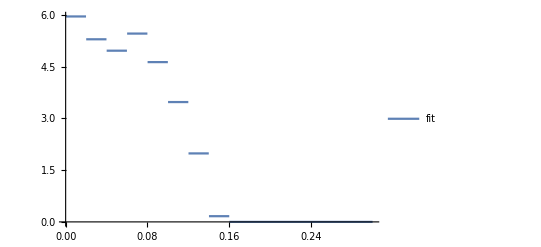

```mathematica
Plot[PDF[qdnear,x],{x,0,0.3},PlotLegends->{"fit"}]
```

```mathematica
𝒟 = UniformDistribution[{0,1}];
```

```mathematica
beta𝒟=FindDistribution[N[p/q]]
```

UniformDistribution[{0.0000150775,0.999996}]

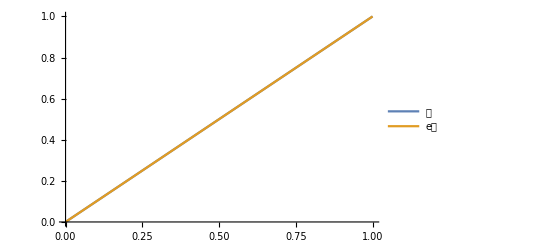

```mathematica
Plot[{CDF[𝒟,x],CDF[beta𝒟,x]},{x,0,1},PlotLegends->{"𝒟","e𝒟"},PlotRange->All]
```

```mathematica
qdata = N[q/10^9];
```

```mathematica
q𝒟=FindDistribution[qdata]
```

MixtureDistribution[{0.525065,0.474935},{NormalDistribution[0.381889,0.227208],NormalDistribution[0.868324,0.108967]}]

```mathematica
x = .;
```

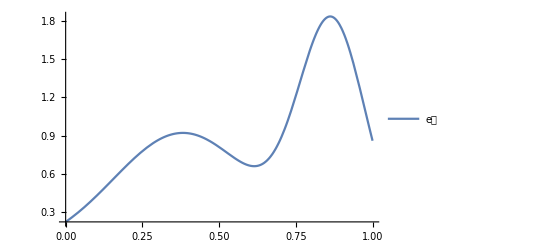

```mathematica
Plot[PDF[q𝒟,x],{x,0,1},PlotLegends->{"e𝒟"}]
```

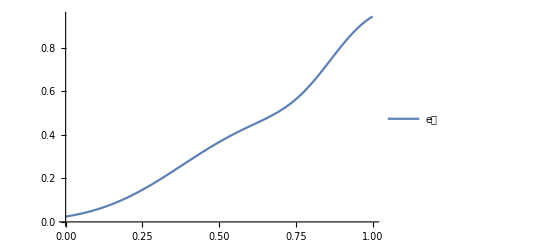

```mathematica
Plot[{CDF[q𝒟,x]},{x,0,1},PlotLegends->{"e𝒟"}]
```

```mathematica
Xint =Interpolation[ParallelTable[{CDF[q𝒟,z],z},{z,0.,1.,1./10000}]]
```

InterpolatingFunction[…]

```mathematica
Xint[0.25]
```

0.368286

InterpolatingFunction::dmval: Input value {0.0000204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

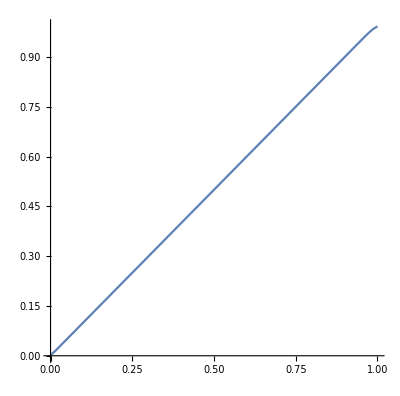

```mathematica
ParametricPlot[{w, CDF[q𝒟,Xint[w]]},{w,0,1}]
```

InterpolatingFunction::dmval: Input value {0.0000204082} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

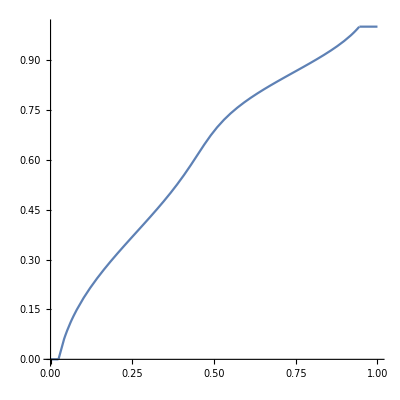

```mathematica
With[{M = 10^9},ParametricPlot[{ r, Clip[Xint[r],{0,1}]}, {r,0.,1.}]]
```

```mathematica
NIntegrate[Re[PP//.{M->10^9,Q ->M Xint[w], ϵ-> Pi(1-2 w)}],{w,0.1, 0.9}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.